```mathematica
Options[Singularity]={Angle->Pi/3,Even->True};
Singularity[pt1_List,pt2_List,width_,options___]:=Line[Module[{vecL,vecT,n,
length=Sqrt[(pt2-pt1).(pt2-pt1)],
relangle=Angle/.Flatten[{options},1]/.Options[Singularity],
even=Even/.Flatten[{options},1]/.Options[Singularity]},
n=Round[length/(2width Tan[relangle/2])]+If[even,0,1];
vecL=(pt2-pt1)/n;
vecT={-#1,#2}&@@Reverse[vecL];
vecT=vecT/Sqrt[vecT.vecT]width;
{pt1}~Join~{pt1+vecL}~Join~Table[pt1+(i+1/2) vecL-(-1)^i vecT,{i,1,n-2}]~Join~{pt2-vecL}~Join~{pt2}
]]
```

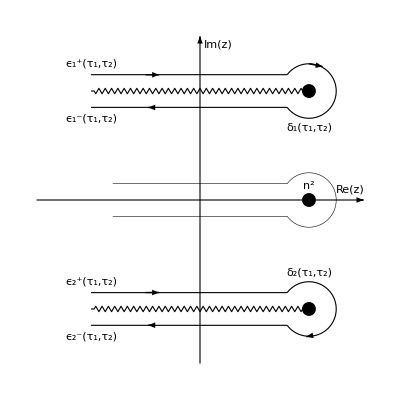

```mathematica
Show[Graphics[{
{Thickness[.002],Line[{{0,0},{0,3}}]},
{Thickness[.002],Line[{{0,0},{0,-3}}]},
{Thickness[.002],Line[{{3,0},{0,0}}]},
{Thickness[.002],Line[{{-3,0},{0,0}}]},
{PointSize[.025],Black,Point[{2,2}]},
{PointSize[.025],Black,Point[{2,-2}]},
{PointSize[.025],Black,Point[{2,0}]},
{Thickness[.002],Circle[{2,2},.5,{-2.50,2.50}]},
{Thickness[.002],Circle[{2,-2},.5,{-2.50,2.50}]},
{Thickness[.002],Line[{{1.60,2.30},{-2,2.30}}]},
{Thickness[.002],Line[{{1.60,1.70},{-2,1.70}}]},
{Thickness[.002],Line[{{1.60,-2.30},{-2,-2.30}}]},
{Thickness[.002],Line[{{1.60,-1.70},{-2,-1.70}}]},
{Thickness[.002],Black,Singularity[{2,2},{-2,2},.05]},
{Thickness[.002],Black,Singularity[{-2,-2},{2,-2},.05]},
{Arrowheads[.025],Arrow[{{0,2.95},{0,3}}]},
{Arrowheads[.025],Arrow[{{2.95,0},{3,0}}]},
{Arrowheads[.025],Arrow[{{2,2.5},{2.25,2.45}}]},
{Arrowheads[.025],Arrow[{{2,-2.50},{1.95,-2.51}}]},
{Arrowheads[.025],Arrow[{{-1,2.2980},{-0.75,2.2980}}]},
{Arrowheads[.025],Arrow[{{-1,-2.2980+0.60},{-0.75,-2.2980+0.60}}]},
{Arrowheads[.025],Arrow[{{-0.90,-2.2980},{-0.95,-2.2980}}]},
{Arrowheads[.025],Arrow[{{-0.90,2.2980-0.6},{-0.95,2.2980-0.6}}]},
Text["n^2",{2,0.25}],Text["Im(z)",{0.33,2.85}],Text["Re(z)",{2.75,0.2}],Text["δ_1(τ_1,τ_2)",{2,1.33}],Text["δ_2(τ_1,τ_2)",{2,-1.33}],Text["ϵ_1^+(τ_1,τ_2)",{-2,2.50}],Text["ϵ_1^-(τ_1,τ_2)",{-2,1.50}],Text["ϵ_2^-(τ_1,τ_2)",{-2,-2.50}],
Text["ϵ_2^+(τ_1,τ_2)",{-2,-1.50}],
{Thickness[.001],Circle[{2,0},.5,{-2.50,2.50}]},
{Thickness[.001],Line[{{1.60,0.30},{-1.6,.30}}]},{Thickness[.001],Line[{{1.60,-0.30},{-1.6,-.30}}]}
                                                 }],
PlotRange->{{-3.00,3.00},{-3.00,3.00}},AspectRatio->Automatic]
```

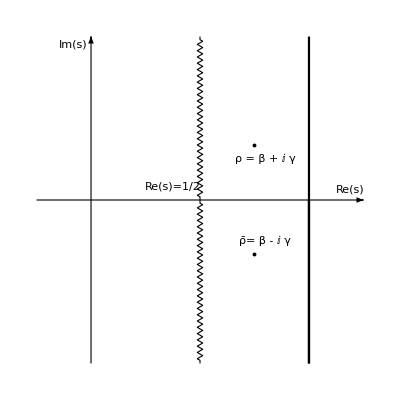

```mathematica
Show[Graphics[{
{Thickness[.002],Line[{{-2,0},{-2,3}}]},
{Thickness[.002],Line[{{-2,0},{-2,-3}}]},
{Thickness[.002],Line[{{-3,0},{3,0}}]},
{Thickness[.004],Line[{{2,0},{2,3}}]},
{Thickness[.004],Line[{{2,0},{2,-3}}]},
{Thickness[.004],Line[{{2,0},{2,-3}}]},
{Thickness[.002],Black,Singularity[{0,0},{0,3},.05]},
{Thickness[.002],Black,Singularity[{0,0},{0,-3},.05]},
{PointSize[.007],Black,Point[{1,1}]},
{PointSize[.007],Black,Point[{1,-1}]},
Text["Re(s)",{2.75,0.2}],{Arrowheads[.025],Arrow[{{-2,2.95},{-2,3}}]},{Arrowheads[.025],Arrow[{{2.95,0},{3,0}}]},Text["Im(s)",{-2.33,2.85}],Text["Re(s)=1/2",{-0.5,0.25}],Text["ρ = β + ⅈ γ",{1.2,0.75}],Text["ρ̄= β - ⅈ γ",{1.2,-0.75}]
                                                 }],
PlotRange->{{-3.00,3.00},{-3.00,3.00}},AspectRatio->Automatic]
```

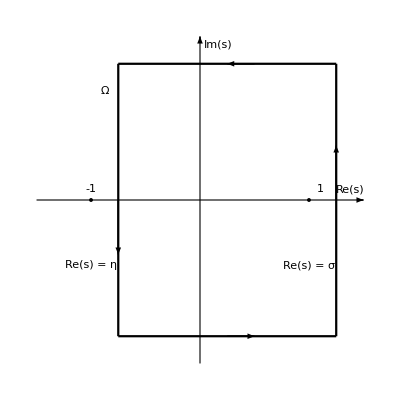

```mathematica
Show[Graphics[{
{Thickness[.002],Line[{{-3,0},{3,0}}]},
{Thickness[.002],Line[{{0,-3},{0,3}}]},
{Thickness[.004],Line[{{-1.5,-2.5},{-1.5,2.5}}]},
{Thickness[.004],Line[{{2.5,-2.5},{2.5,2.5}}]} ,
{Thickness[.004],Line[{{-1.5,-2.5},{2.5,-2.5}}]} ,
{PointSize[.007],Black,Point[{2,0}]},
{PointSize[.007],Black,Point[{-2,0}]},
{Thickness[.004],Line[{{-1.5,2.5},{2.5,2.5}}]} ,Text["Im(s)",{0.33,2.85}],Text["Re(s)",{2.75,0.2}],Text["1",{2.2,0.2}],Text["-1",{-2,0.2}],Text["Re(s) = σ",{2,-1.2}],Text["Ω",{-1.75,2}],Text["Re(s) = η",{-2,-1.2}],{Arrowheads[.025],Arrow[{{0,2.95},{0,3}}]},
{Arrowheads[.025],Arrow[{{2.95,0},{3,0}}]},
{Arrowheads[.025],Arrow[{{2.5,0},{2.5,1}}]},
{Arrowheads[.025],Arrow[{{1,2.5},{0.5,2.5}}]},
{Arrowheads[.025],Arrow[{{-1.5,0},{-1.5,-1}}]},
{Arrowheads[.025],Arrow[{{0.5,-2.5},{1,-2.5}}]}
}],
PlotRange->{{-3.00,3.00},{-3.00,3.00}},AspectRatio->Automatic]
```